```mathematica
Node Clustering based on x, y, r
```

## Reading data

```mathematica
root = "D:/";
```

```mathematica
root = "~/research/posecpp";
home = $HomeDirectory;
```

```mathematica
xvr= ToExpression//@StringSplit/@ReadList[root<>"/geo/converge_x.txt",Record];
yvr= ToExpression//@StringSplit/@ReadList[root<>"/geo/converge_y.txt",Record];
svr= ToExpression//@StringSplit/@ReadList[root<>"/geo/converge_s.txt",Record];
noisyr= ToExpression//@StringSplit/@ReadList[root<>"/geo/converge_n.txt",Record]/.{false->False,true->True};
```

```mathematica
pickFinal[x_]:=x[[;;,{1,-1}]];
```

```mathematica
xvr;
```

```mathematica
xv=pickFinal[xvr];yv=pickFinal[yvr];sv=pickFinal[svr];nv=pickFinal[noisyr];summary=Join[xv,yv,sv,nv,2];
```

```mathematica
#[[1]]==#[[3]]==#[[5]]==#[[7]]&/@summary//Union
```

{True}

## Load Body Part

```mathematica
Gr[fn_]:=Graph[Map[#[[1]]<->#[[2]]&,ReadList[fn,{Number,Number}]],VertexLabels->"Name"];
graph=Gr[root<>"/geo/alt010101.txt"];
headlist = ReadList[home<>"/git/posecpp/res/head_clusters_52.txt"];
comm=FindGraphCommunities[graph];
```

```mathematica
NeighborhoodGraph[graph,417]
```

-Graphics-

```mathematica
graph
```

-Graphics-

```mathematica
Length[Intersection[#,headlist]]&/@comm
```

{0,0,27,0,7,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0}

```mathematica
Length/@comm
```

{80,48,43,35,28,26,26,18,16,15,10,5,4,4,4,4,3,3,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}

```mathematica
HighlightGraph[Subgraph[graph,comm[[3]],VertexLabels->"Name"],headlist]
```

-Graphics-

```mathematica
denoisedSummary = Select[summary,{#
```

```mathematica
headNodeList = {#[[2]]+#[[6]]/2,-#[[4]]-#[[6]]/2}&/@Select[summary,MemberQ[comm[[5]],#[[1]]]&];
```

```mathematica
partedList=Function[x,{#[[2]]+#[[6]]/2,-#[[4]]-#[[6]]/2}&/@Select[summary,MemberQ[x,#[[1]]]&]]/@comm;
```

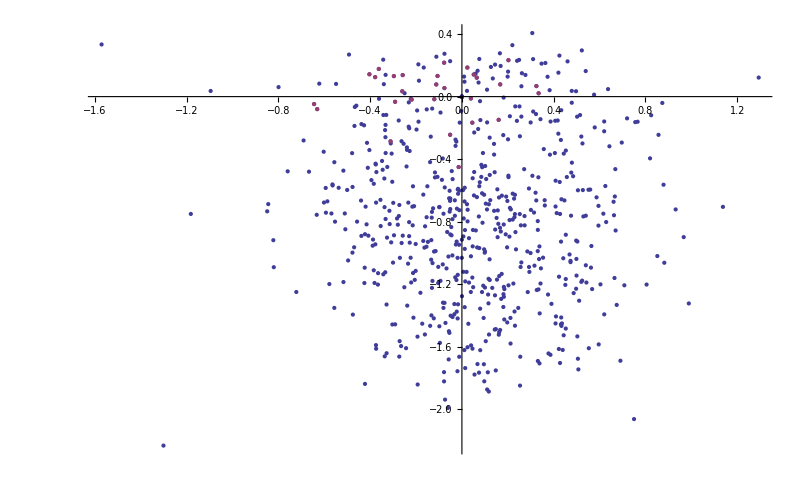

```mathematica
ListPlot[{{#[[2]],-#[[4]]}&/@summary,headNodeList}]
```

```mathematica
badList = {124,392,818,585,542,113};badNodeList = {#[[2]]+#[[6]]/2,-#[[4]]-#[[6]]/2}&/@Select[summary,MemberQ[badList,#[[1]]]&];
```

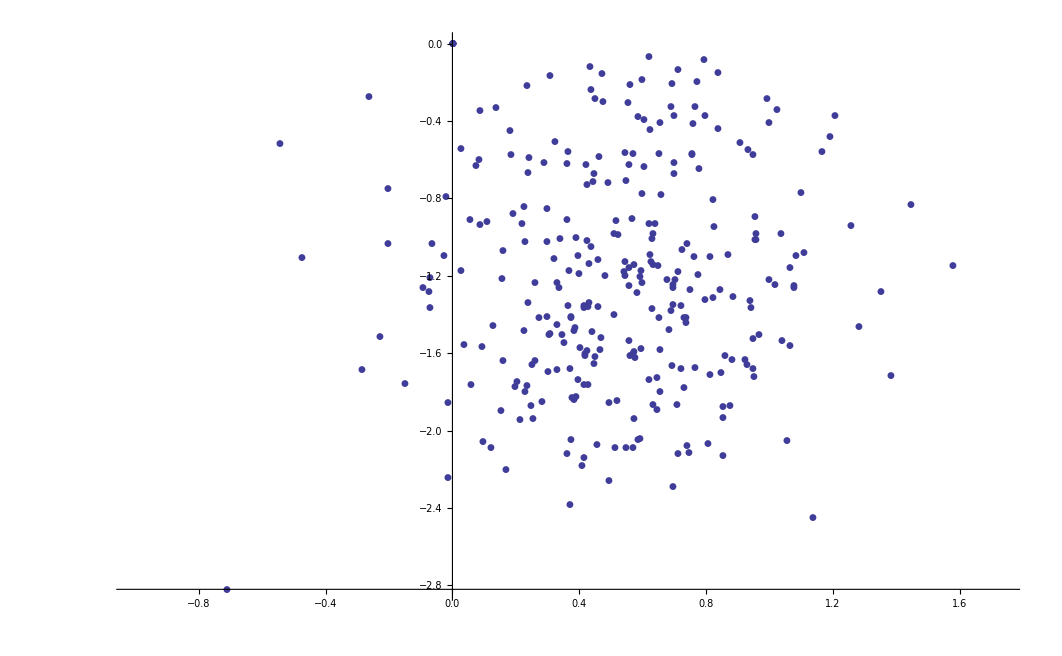

```mathematica
ListPlot[{{#[[2]]+#[[6]]/2,-#[[4]]-#[[6]]/2}&/@summary,headNodeList,badNodeList},PlotMarkers->Automatic]
```

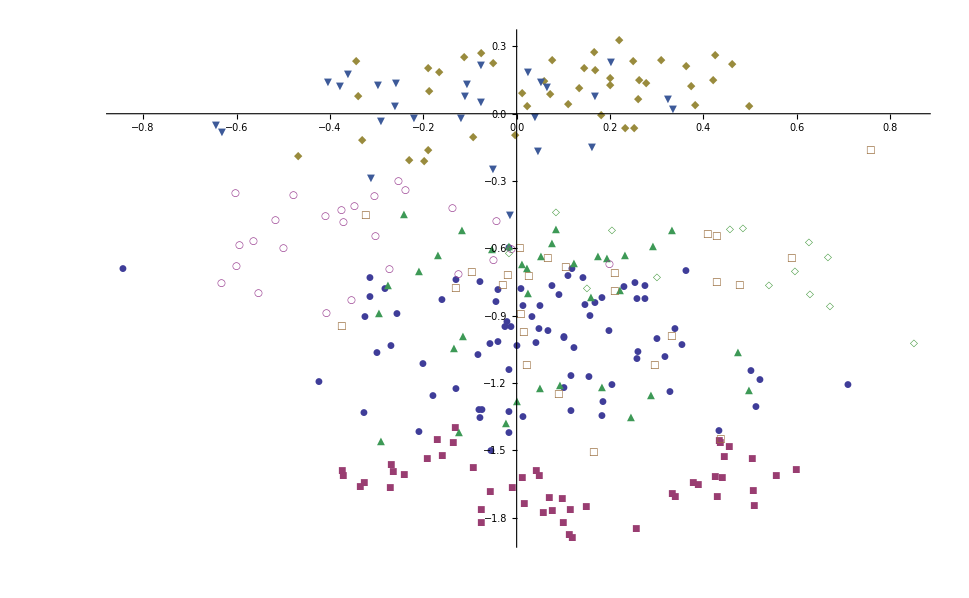

```mathematica
ListPlot[partedList,PlotMarkers->Automatic]
```

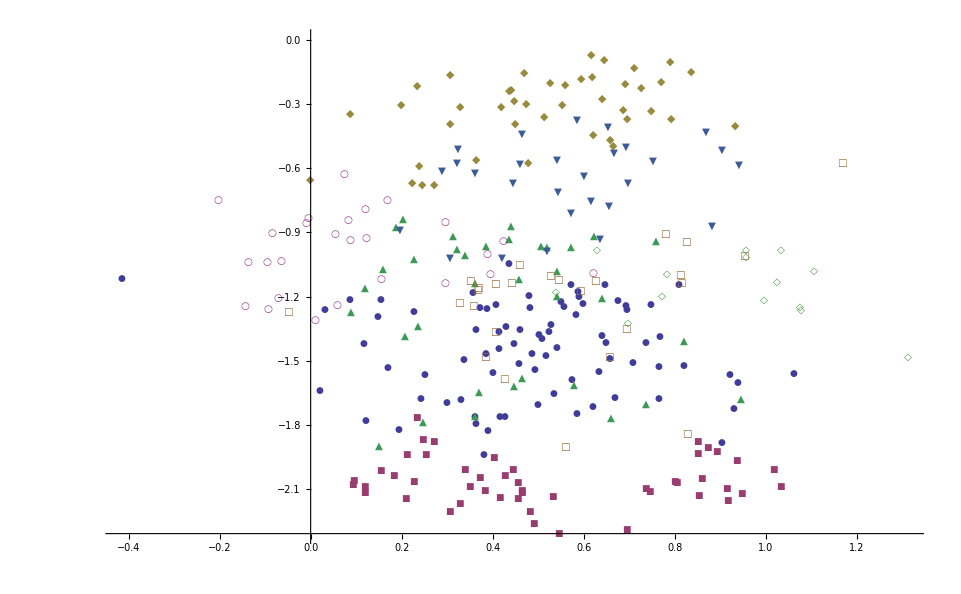

```mathematica
ListPlot[partedList,PlotMarkers->Automatic]
```

```mathematica
partedList//Length
```

34

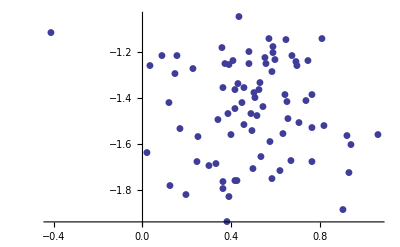
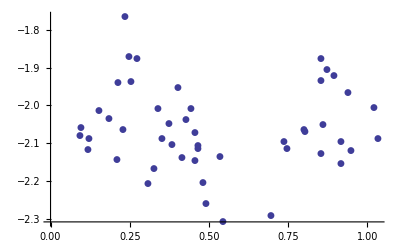
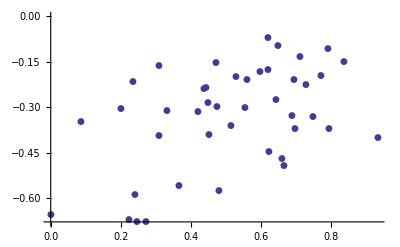
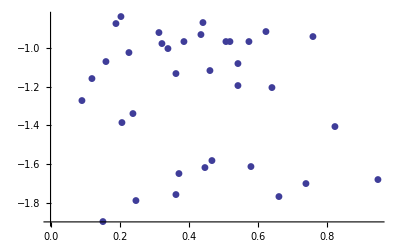
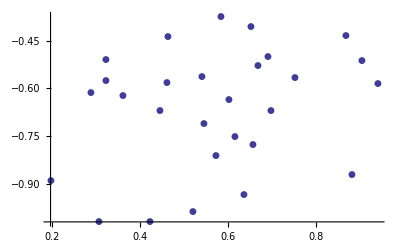
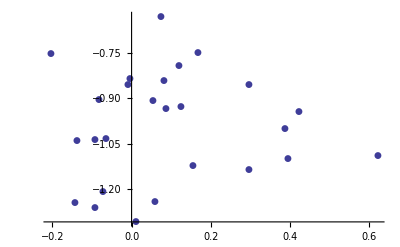
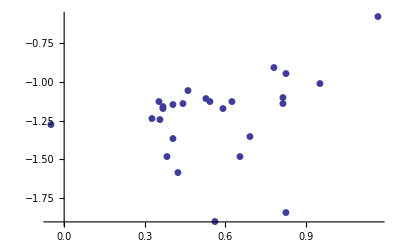
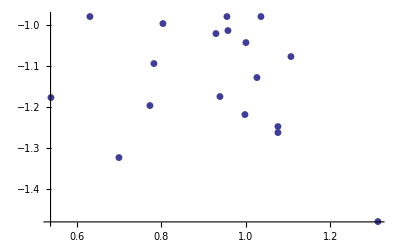

```mathematica
Table[ListPlot[partedList[[i]],PlotMarkers->Automatic],{i,1,34}]
```

```mathematica
comm[[2]]
```

{37,63,545,436,104,141,216,478,549,953,963,279,509,532,765,257,272,651,686,714,660,383,368,461,778,404,409,600,767,889,899,756,883,659,664,849,887,460,631,596,969,831,920,937,812,701,731,905}

```mathematica
comm[[8]]
```

{193,290,957,246,425,443,534,288,430,808,919,737,328,403,493,611,997,633}

```mathematica
comm[[1]]
```

{15,358,29,220,309,410,647,797,42,245,108,166,173,677,722,727,519,860,386,412,579,177,316,332,372,736,185,875,563,211,512,990,212,329,431,1000,271,292,318,548,757,895,952,348,352,501,525,578,583,891,825,378,710,827,949,575,646,815,915,956,688,775,606,601,530,642,970,804,816,820,634,776,671,753,580,851,624,639,707,1003}

```mathematica
comm[[4]]
```

{54,518,68,554,114,640,120,196,268,598,195,492,852,929,961,252,587,253,558,819,988,269,539,424,486,917,922,700,844,719,962,885,725,955,918}